```mathematica
sys={3x-y==1; 2x+3y==-1};
```

```mathematica
X={{0,0},{1/3,-1/3},{2/9,-5/9},{4/27,-13/27},{14/81,-35/81}};
```

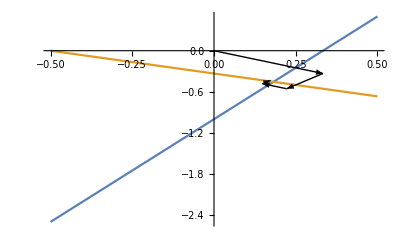

```mathematica
Show[Plot[{3x-1,1/3(-2x-1)},{x,-0.5,0.5}],Graphics[Table[{Arrowheads[0.015],Arrow[{X[[i]],X[[i+1]]}]},{i,1,4}]]]
```

```mathematica
f[y_]:=1/2(-3 y-1)
```

```mathematica
g[x_]:=3 x-1
```

```mathematica
f[0]
```

-1/2

```mathematica
g[0]
```

-1

```mathematica
f[-1]
```

1

```mathematica
g[-1/2]
```

-5/2

```mathematica
f[1]
```

-2

```mathematica
g[-5/2]
```

-17/2

```mathematica
f[52/27]
```

50/81

```mathematica
g[-20/27]
```

131/81

```mathematica
{{a11,0,0},{a21,a22,0},{a31,a32,a33}}//MatrixForm
```

(a11 | 0 | 0
a21 | a22 | 0
a31 | a32 | a33)

```mathematica
FullSimplify[Dot[Inverse[{{a11,0,0},{a21,a22,0},{a31,a32,a33}}],{{0,-a12,-a13},{0,0,-a23},{0,0,0}}]]
```

{{0,-a12/a11,-a13/a11},{0,(a12 a21)/(a11 a22),(a13 a21-a11 a23)/(a11 a22)},{0,(a12 (a22 a31-a21 a32))/(a11 a22 a33),(a13 a22 a31-a13 a21 a32+a11 a23 a32)/(a11 a22 a33)}}